```mathematica
csvInput =Import["/Users/hans/Library/Developer/Xcode/DerivedData/AudioFiltersXcodeProject-gurxbpoxiecbajamniswkxrsbpnq/Build/Products/Debug/arrayOut.csv"];
sound = ListPlay[#[[2]]&/@csvInput,SampleRate->48000,PlayRange->All];
```

```mathematica
Export["~/Desktop/test.wav",sound]
```

~/Desktop/test.wav

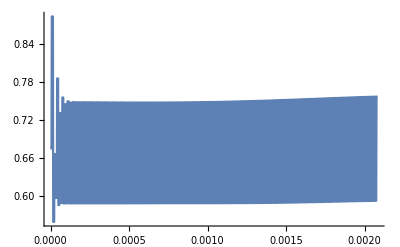

```mathematica
ListLinePlot[csvInput[[1;;1000]],PlotRange->All]
```